```mathematica
ordindex[λ_]:=√(2.7359+0.01878/(λ λ-0.01822)-0.01354 λ λ);
extindex[λ_]:=√(2.3753+0.01224/(λ λ-0.01667)-0.01516 λ λ);
airindex[λ_]:=1.000287566+1.3412/((10^18 (λ λ))/10^12);
λp=0.405; (*// in um //*)
λd=λp*2; (* degenerate SPDC *)

nop=ordindex[λp]^2
nep=extindex[λp]^2
nod=ordindex[λd]^2
ned=extindex[λd]^2

θdeg=ArcCos[Sqrt[(nep/nod -1)*(nop/(nep-nop))]]*180/π
```

2.86248

2.45588

2.75646

2.3845

28.8159

```mathematica
λp=0.405;
λs=0.760;
λi=λs*λp/(λs-λp);

nop=ordindex[λp];
nep=extindex[λp];

nos=ordindex[λs];
nes=extindex[λs];
nairs=airindex[λs];

noi=ordindex[λi];
nei=extindex[λi];
nairi=airindex[λi];

Θ=ArcCos[Sqrt[(λs^2*λi^2/(λp^2*(λi*nos +λs*noi)^2) -1/nep^2)*(nop^2*nep^2)/(nep^2-nop^2)]]*180/π
```

28.7591

```mathematica
Clear[a,b,c,d,e,x,λs,λi,λp,nos,noi,nop,nes,nei,nep,Θs,Θp];

λp=0.405;
λs=0.760;
λi=λs*λp/(λs-λp);
c=2.989*10^8;
ωp=2*π*c*1000000/λp;
ωs=2*π*c*1000000/λs;
ωi=2*π*c*1000000/λi;
Θp=28.7591*π/180;

nop=ordindex[λp];
nep=extindex[λp];
npeff=Sqrt[1/((Cos[Θp]/nop)^2 + (Sin[Θp]/nep)^2)];

nos=ordindex[λs];
nes=extindex[λs];
nairs=airindex[λs];

noi=ordindex[λi];
nei=extindex[λi];
nairi=airindex[λi];


a=npeff*ωp/(noi*ωi);
b=nos*ωs/(noi*ωi);
c=nos;
d=nos*nos + (ωp*npeff/ωs)^2;
e=2*ωp*npeff*nos/ωs;
SolnList=NSolve[c-d+a^2 d-2 a b d x+e x-a^2 e x-c x^2+b^2 d x^2+2 a b e x^2-b^2 e x^3==0,x];
corr=x/.SolnList[[1]];
corr=If[corr<1,corr,1];
ArcCos[corr]*180/π;
(*after entering air*)
ArcSin[Sin[ArcCos[corr]]*noi/nairi]*180/π
SolnList
```

0.

{{x→1.},{x→1.4304},{x→2.4007}}

/home/qitlab/Documents/SPDCexitangle.csv

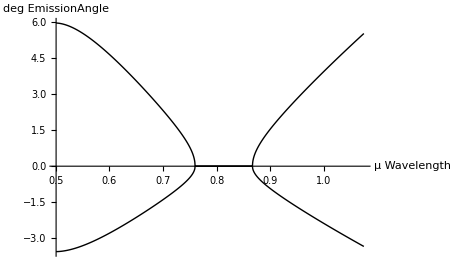

```mathematica
startλ=0.5;
interval=0.0005;

emissionfinder[incangle_,incre_]:=Module[{theta,λp,λs,λi,nop,nep,nos,nes,noi,nei,npeff,Θp,ωp,ωs,ωi,a,b,c,d,e,SolnList,corr},

λp=0.405;

startλ=0.5;
interval=0.0005;

λs=startλ+(incre *interval);
λi=(λs λp)/(λs-λp);

c=2.989 10^8;
ωp=(2 π c 1000000)/λp;
ωs=(2 π c 1000000)/λs;
ωi=(2 π c 1000000)/λi;

Θp=(incangle π)/180;

nop=ordindex[λp];
nep=extindex[λp];
npeff=√(1/((Cos[Θp]/nop)^2+(Sin[Θp]/nep)^2));

nos=ordindex[λs];
nes=extindex[λs];
nairs=airindex[λs];

noi=ordindex[λi];
nei=extindex[λi];
nairi=airindex[λi];

a=(npeff ωp)/(noi ωi);
b=(nos ωs)/(noi ωi);
c=nos;
d=nos nos+((ωp npeff)/ωs)^2;
e=(2 ωp npeff nos)/ωs;SolnList=NSolve[c-d+a^2 d-2 a b d x+e x-a^2 e x-c x^2+b^2 d x^2+2 a b e x^2-b^2 e x^3==0,x];

corr=x/.SolnList⟦1⟧;

corr=If[corr<1,corr,1];

theta=(ArcCos[corr] 180)/π;
theta=(Sin[ArcCos[corr]] nos 180)/(nairs π);

Return[theta];];


negemissionfinder[incangle_,incre_]:=Module[{theta,λp,λs,λi,nop,nep,nos,nes,noi,nei,npeff,Θp,ωp,ωs,ωi,a,b,c,d,e,SolnList,corr},

λp=0.405;

startλ=0.5;
interval=0.0005;

λs=startλ+(incre *interval);
λi=(λs λp)/(λs-λp);

c=2.989 10^8;
ωp=(2 π c 1000000)/λp;
ωs=(2 π c 1000000)/λs;
ωi=(2 π c 1000000)/λi;

Θp=(incangle π)/180;

nop=ordindex[λp];
nep=extindex[λp];
npeff=√(1/((Cos[Θp]/nop)^2+(Sin[Θp]/nep)^2));

nos=ordindex[λs];
nes=extindex[λs];
nairs=airindex[λs];

noi=ordindex[λi];
nei=extindex[λi];
nairi=airindex[λi];

a=(npeff ωp)/(noi ωi);
b=(nos ωs)/(noi ωi);
c=nos;
d=nos nos+((ωp npeff)/ωs)^2;
e=(2 ωp npeff nos)/ωs;
SolnList=NSolve[c-d+a^2 d-2 a b d x+e x-a^2 e x-c x^2+b^2 d x^2+2 a b e x^2-b^2 e x^3==0,x];corr=x/.SolnList⟦1⟧;corr=If[corr<1,corr,1];
theta=-(ArcCos[corr] 180)/π;
Return[theta];];

datapoints=1150;

Clear[thetalist,negthetalist,index,incangle];

thetalist=Table[0,{i,datapoints}];
negthetalist=Table[0,{i,datapoints}];
incangle=28.7591;

For[index=1,index<(datapoints+1),thetalist⟦index⟧=emissionfinder[incangle,index];index++;];

DataTable=Table[{startλ+(i *interval),thetalist⟦i⟧},{i,datapoints}];
Export["/home/qitlab/Documents/SPDCexitangle.csv",DataTable]
For[index=1,index<(datapoints+1),negthetalist⟦index⟧=negemissionfinder[incangle,index];index++;];
DataTable1=Table[{startλ+(i* interval),negthetalist⟦i⟧},{i,datapoints}];
(*ListPlot[{DataTable,DataTable1},AxesLabel->{Wavelength μ,EmissionAngle deg}];*)
ListPlot[{DataTable,DataTable1},Joined->True,PlotStyle->Black,AxesLabel->{Wavelength μ,EmissionAngle deg}]
```

0.999968

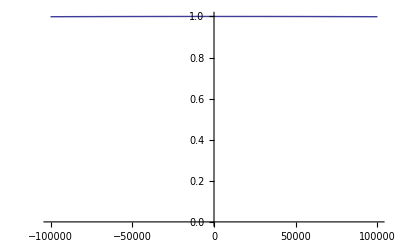

```mathematica
λp=0.405;
λs=0.760;
λi=λs*λp/(λs-λp);
c=2.989*10^8;
ωp=2*π*c*1000000/λp;
ωs=2*π*c*1000000/λs;
ωi=2*π*c*1000000/λi;
nop=ordindex[λp];
nep=extindex[λp];
npeff=Sqrt[1/((Cos[Θp]/nop)^2 + (Sin[Θp]/nep)^2)];

nos=ordindex[λs];
nes=extindex[λs];

noi=ordindex[λi];
nei=extindex[λi];

Θp=28.7591*π/180;
Θi=0.0*π/180;
Θs=Θi;

L=15760; (*length of crystal in um*)
W=76.5;(*waist of pump in um*)

δkz=(npeff*ωp -nos*ωs*Cos[Θs] - noi*ωi*Cos[Θi])/(c*1000000);
δkx=(nos*ωs*Sin[Θs] - noi*ωi*Sin[Θi])/(c*1000000);
δky=(-nos*ωs*Sin[Θs] - noi*ωi*Sin[Θi])/(c*1000000);

Φ=Exp[-W^2(δkx^2 + δky^2)/2]*(Sin[δkz*L/2]/(δkz*L/2))^2
Plot[Exp[-W^2(δkx^2 + δky^2)/2]*(Sin[δkz*L/2]/(δkz*L/2))^2,{L,-100000,100000},PlotRange->{0,1}]
```

```mathematica
phasefunction[thetas_,λs_]:=Module[{Φ,λp,λi,c,nop,nep,nos,nes,noi,nei,npeff,ωp,ωs,ωi,Θp,Θs,Θi,L,W,δkz,δky,δkx},λp=0.405;λi=λs*λp/(λs-λp);
nop=ordindex[λp];nep=extindex[λp];
nos=ordindex[λs];nes=extindex[λs];noi=ordindex[λi];nei=extindex[λi];
Θp=29.80*π/180;
Θs=thetas*π/180;
Θi=ArcSin[nos*ωs*Sin[Θs]/(noi*ωi)];
ωp=2*π/λp;ωs=2*π/λs;ωi=2*π/λi;
npeff=Sqrt[1/((Cos[Θp]/nop)^2+(Sin[Θp]/nep)^2)];
L=15760;(*length of crystal*)
W=76;(*waist of pump*)
δkz=(npeff*ωp-nos*ωs*Cos[Θs]-noi*ωi*Cos[Θi]);
δkx=0;
δky=(-nos*ωs*Sin[Θs]+noi*ωi*Sin[Θi]);
Φ=Exp[-W^2(δkx^2+δky^2)/2]*(Sin[δkz*L/2]/(δkz*L/2))^2;
Return[Φ];];
ListDensityPlot[Table[phasefunction[x,y],{x,-2,2,0.05},{y,0.65,0.95,0.001}],Mesh->False,PlotRange->{0,1}]
```